# Fibonacci

```mathematica
fib=Table[0,20000];
```

```mathematica
SetSharedVariable@fib
```

```mathematica
ParallelDo[fib[[x]]=Length@Divisors[Fibonacci[x]],{x,20000}]
```

```mathematica
Export["fib.csv", fib]
```

fib.csv

```mathematica
Table[Fibonacci[x],{x,10}]
```

{1,1,2,3,5,8,13,21,34,55}

```mathematica
Fibonacci[500]//IntegerDigits//Length
```

105

```mathematica
horizontalQ[a_Integer, b_Integer, ts_List]:=Block[{result=True},
	Do[
		If[ts[[x]] < ts[[a]] && ts[[x]] < ts[[b]],result=True,result=False;Return[False]],
		{x,a+1,b-1}
	];
	Return[result]
]
```

```mathematica
visibleQ[a_Integer, b_Integer, ts_List]:=Block[{result=True},
	Do[
		If[ts[[x]] >= ts[[a]]+(ts[[b]]−ts[[a]])(x−a)/(b−a),result=False;Return[]],
		{x,a+1,b-1}
	];
	result
]
```

```mathematica
naturalVisibility[series_]:=Block[{visibles},
	visibles={};
	Do[
		Do[
			If[visibleQ[i,j,series],AppendTo[visibles,i->j],Null],
			{j,i+1,Length@series}
		],
		{i,1,Length@series-1}
	];
	Return[visibles]
]
```

```mathematica
horizontalVisibility[series_]:=Block[{visibles},
	visibles={};
	Do[
		Do[
			If[horizontalQ[i,j,series],AppendTo[visibles,i->j],Null],
			{j,i+1,Length@series}
		],
		{i,1,Length@series-1}
	];
	Return[visibles]
]
```

```mathematica
naturalStats[series_]:=Block[{links,degrees,g,nlm},
	links=naturalVisibility[series];
	g=Graph[links[[2;;]]];
	degrees=Counts[VertexDegree[g]]/Length@VertexDegree[g];
	nlm=NonlinearModelFit[Table[{c,Lookup[degrees,c]},{c,Keys[degrees]}],C x^-γ,{γ,C},x];
	nlm["ParameterConfidenceIntervalTable"]
]
```

```mathematica
horizontalStats[series_]:=Block[{links,degrees,g,nlm},
	links=horizontalVisibility[series];
	g=Graph[links[[2;;]]];
	degrees=Counts[VertexDegree[g]]/Length@VertexDegree[g];
	nlm=NonlinearModelFit[Table[{c,Lookup[degrees,c]},{c,Keys[degrees]}],C x^-γ,{γ,C},x];
	nlm["ParameterConfidenceIntervalTable"]
]
```

```mathematica
orbit[x_]:=Block[{d=0,n=x},
While[n>2,n=Length@Divisors[n];d+=1;];
Return[d]
]
```

## Divisors

```mathematica
series=fib[[;;500]];
```

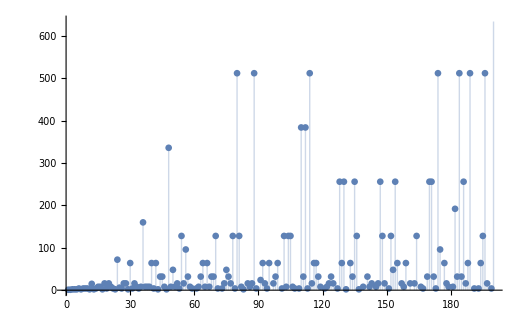

```mathematica
ListPlot[series[[;;200]],Filling->Axis]
```

### Convergence of mean degree and mean distance

```mathematica
sdl[vals_List]:=Block[{diffs,counts,Hmax,H,delta},
diffs=Differences[vals];
counts=Counts[#]/Length@diffs&@diffs;
Hmax=Log[Length@counts];
H=-Total[# Log[#]&/@counts]//N;
delta=H/Hmax;
{4 delta(1-delta),delta}//N
]
```

```mathematica
sdl[series]
```

{0.188235,0.95049}

## Visibility graphs

## Natural Visibility

```mathematica
fibNVLinks=naturalVisibility[series];
```

```mathematica
fibNVGraph=Graph[fibNVLinks,DirectedEdges->False,VertexLabels->"Name",GraphLayout->"CircularEmbedding"];
```

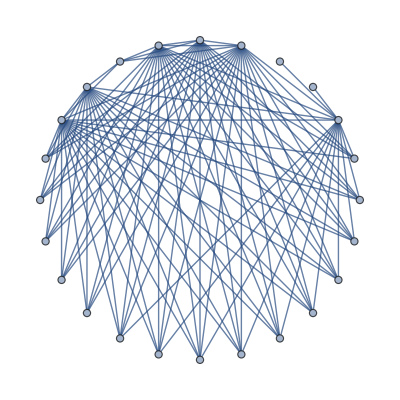

```mathematica
Graph[fibNVLinks[[;;100]],DirectedEdges->False,GraphLayout->"CircularEmbedding"]
```

```mathematica
fibNVDegrees=Counts[VertexDegree[fibNVGraph]]/Length@VertexDegree[fibNVGraph]
```

<|19→7/500,18→3/125,20→1/125,22→1/250,30→1/500,39→1/500,41→1/500,45→1/250,64→1/500,62→1/500,46→1/500,63→1/500,143→1/500,150→1/500,162→1/500,238→1/500,102→1/500,412→1/500,231→1/500,308→1/500,17→1/125,14→19/500,15→3/125,16→7/500,13→17/500,12→3/50,23→1/250,10→7/100,11→31/500,6→51/500,8→3/25,9→9/100,25→1/100,7→13/100,38→1/500,26→3/250,5→41/500,3→3/500,21→3/500,55→1/500,4→4/125,27→1/500,32→1/500,52→1/500,24→1/500|>

```mathematica
data=Table[{x,fibNVDegrees[x]},{x,Keys[fibNVDegrees]}];
fibNVNlm=NonlinearModelFit[data,c k^-γ E^(-d k),{{γ,2},{c,3},{d,0}},k]
```

FittedModel[0.000271497 ⅇ^(-0.80616 k) k^6.00465]

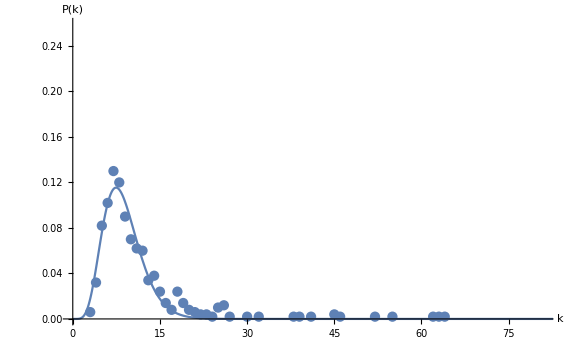

```mathematica
fibNVPlot=Show[
ListPlot[fibNVDegrees,PlotRange->{{0,81},{0,0.259}},AxesOrigin->{0,0}],
Plot[fibNVNlm[x],{x,0,Max[Keys[fibNVDegrees]]},PlotRange->{{0,81},{0,0.26}},AxesOrigin->{0,0}],
AxesLabel-> {Style["k",36, Italic],Style["P(k)", 36,Italic]},LabelStyle->20,ImageSize->Large
]
```

```mathematica
fibNVNlm["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
γ | -6.00465 | 0.505682 | {-7.02515,-4.98414}
c | 0.000271497 | 0.000146874 | {-0.0000249072,0.000567902}
d | 0.80616 | 0.0638114 | {0.677383,0.934937}

```mathematica
TableForm[Flatten[{"natural visibility",Mean@ VertexDegree[fibNVGraph]//N,MeanGraphDistance[fibNVGraph]//N,
GlobalClusteringCoefficient[fibNVGraph]//N,Mean[fibNVNlm["FitResiduals"]^2],ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@fibNVNlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}],TableHeadings->{{"algo","⟨k⟩","⟨l_min⟩","C_c","⟨e^2⟩","γ","C","δ"}, None},TableDirections->Row]
```

algo | ⟨k⟩ | ⟨l_min⟩ | C_c | ⟨e^2⟩ | γ | C | δ
natural visibility | 14.188 | 2.08964 | 0.141642 | 0.0000512414 | -6.00465 ± 1.02051 | 0.000271497 ± 0.000296404 | 0.80616 ± 0.128777

## Horizontal Visibility

```mathematica
fibHVLinks=horizontalVisibility[series];
```

```mathematica
fibHVGraph=Graph[fibHVLinks,DirectedEdges->False,VertexLabels->"Name",GraphLayout->"CircularEmbedding"];
```

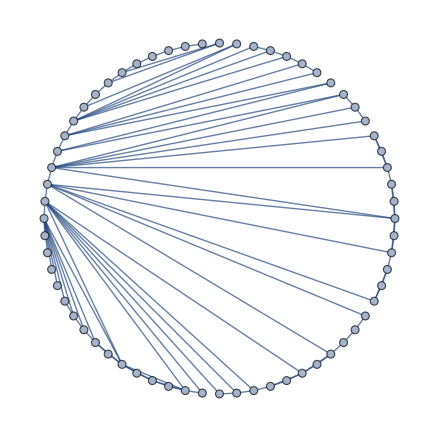

```mathematica
Graph[fibHVLinks[[;;100]],DirectedEdges->False,GraphLayout->"CircularEmbedding"]
```

```mathematica
fibHVDegrees=Counts[VertexDegree[fibHVGraph]]/Length@VertexDegree[fibHVGraph]
```

<|1→1/500,2→2/5,3→29/125,6→11/250,5→43/500,4→63/500,8→2/125,7→4/125,9→13/500,12→1/125,11→3/500,13→1/250,10→3/250,18→1/500,14→1/250|>

```mathematica
fibHVDegrees[1]=.
```

```mathematica
data=Table[{x,fibHVDegrees[x]},{x,Keys[fibHVDegrees]}];
fibHVNlm=NonlinearModelFit[data,c k^-γ E^(-d k),{{γ,2},{c,3},{d,0}},k]
```

FittedModel[(1.20566 ⅇ^(-0.379862 k))/k^0.490378]

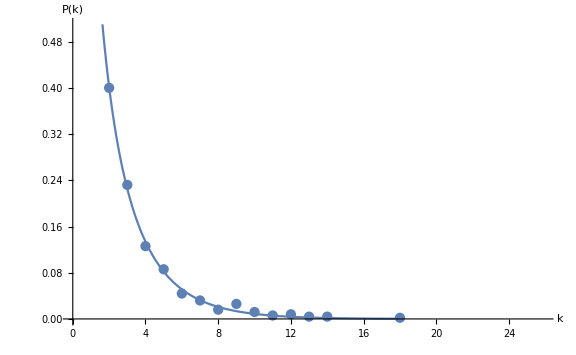

```mathematica
fibHVPlot=Show[
ListPlot[fibHVDegrees,PlotRange->{{0,25.9},{0,.51}},AxesOrigin->{0,0}],Plot[fibHVNlm[x],{x,0,Max[Keys[fibHVDegrees]]},PlotRange->{{0,25},{0,0.51}},AxesOrigin->{0,0}],
AxesLabel-> {Style["k",36, Italic],Style["P(k)", 36,Italic]},LabelStyle->20,ImageSize->Large
]
```

```mathematica
fibHVNlm["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
γ | 0.490378 | 0.199579 | {0.0511086,0.929648}
c | 1.20566 | 0.0501408 | {1.0953,1.31602}
d | 0.379862 | 0.0616382 | {0.244197,0.515526}

```mathematica
TableForm[
Flatten[{"horizontal visibility",Mean@ VertexDegree[fibHVGraph]//N,MeanGraphDistance[fibHVGraph]//N,
GlobalClusteringCoefficient[fibHVGraph]//N,Mean[fibHVNlm["FitResiduals"]^2],ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@fibHVNlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}],TableHeadings->{{"algo","⟨k⟩","⟨l_min⟩","C_c","⟨e^2⟩","γ","C","δ"},None},TableDirections->Row]
```

algo | ⟨k⟩ | ⟨l_min⟩ | C_c | ⟨e^2⟩ | γ | C | δ
horizontal visibility | 3.708 | 9.26409 | 0.301998 | 0.0000285214 | 0.490378 ± 0.43927 | 1.20566 ± 0.110359 | 0.379862 ± 0.135665

## Orbits

```mathematica
orbits=orbit/@series
```

{0,0,0,0,0,2,0,2,2,2,0,3,0,2,3,3,0,2,2,2,3,2,0,5,3,2,2,2,0,2,2,2,3,2,3,5,3,3,3,2,2,2,0,4,4,3,0,5,3,4,3,2,2,4,2,5,4,3,2,5,2,3,4,2,3,2,3,4,4,4,2,5,2,2,4,4,2,4,2,4,4,3,0,5,2,3,2,4,2,5,4,2,2,2,2,4,2,4,2,5,2,4,3,4,4,3,2,5,2,3,4,3,2,4,2,2,2,4,3,4,2,3,2,4,2,5,2,3,2,3,0,5,2,4,3,4,0,2,3,5,4,3,2,5,3,2,3,4,2,5,2,4,4,3,2,5,2,3,2,5,2,2,2,4,2,3,2,5,4,3,3,4,2,4,5,2,2,2,3,5,3,4,4,4,4,3,2,2,4,5,2,5,2,2,4,4,2,4,2,4,4,4,4,5,2,2,4,5,2,2,2,4,4,2,2,5,3,4,2,4,2,2,2,5,3,3,2,5,4,5,3,4,3,2,3,3,2,3,2,5,3,2,4,4,2,3,4,4,2,2,2,4,4,4,4,2,3,5,4,4,5,2,3,4,2,2,4,4,2,5,2,4,5,3,3,5,2,2,3,5,3,4,2,4,5,4,2,2,4,3,4,4,2,3,4,2,2,4,3,6,3,4,4,2,4,5,2,4,3,5,2,5,2,2,2,3,3,2,4,3,2,2,2,3,5,4,2,4,4,4,2,4,4,2,4,6,3,3,2,3,2,5,2,4,5,2,4,5,2,5,5,2,2,2,3,2,4,2,0,5,2,2,4,5,4,4,4,4,2,4,4,5,4,3,5,2,4,4,2,2,4,4,3,6,2,4,5,5,3,4,2,4,2,2,4,5,2,4,5,4,2,2,4,4,4,5,2,5,2,2,2,4,4,4,4,3,2,4,3,5,2,2,4,2,3,2,2,2,2,2,0,5,0,4,4,3,2,2,4,4,2,3,4,6,4,2,4,5,0,5,4,3,2,2,5,4,3,4,4,5,4,2,3,3,4,2,2,4,5,5,3,4,3,5,4,3,4,4,3,5,3,2,5,2,5,2,2,5,4,2,3,5,2,2,2,2,4,2,2,5}

```mathematica
sdl[orbits]
```

{0.582263,0.823163}

## Visibility graphs

## Natural Visibility

```mathematica
fibOrbitsNVLinks=naturalVisibility[orbits];
```

```mathematica
fibOrbitsNVGraph=Graph[fibOrbitsNVLinks,DirectedEdges->False,GraphLayout->"CircularEmbedding"];
```

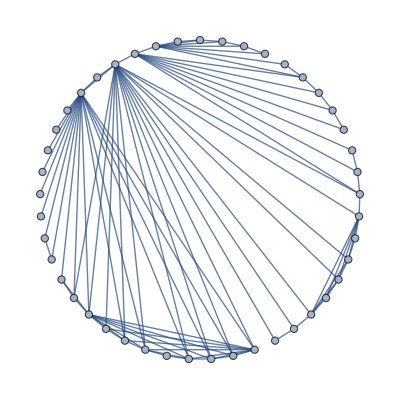

```mathematica
Graph[fibOrbitsNVLinks[[;;100]],DirectedEdges->False,GraphLayout->"CircularEmbedding"]
```

```mathematica
fibOrbitsNVDegrees=Counts[VertexDegree[fibOrbitsNVGraph]]/Length@VertexDegree[fibOrbitsNVGraph]
```

<|2→27/125,3→27/125,8→11/500,4→17/100,9→1/25,19→3/500,7→23/500,5→63/500,6→41/500,11→7/500,52→1/500,10→13/500,13→7/500,15→3/500,12→1/500,16→1/500,26→1/500,27→1/500,14→1/500,17→1/500,32→1/500|>

```mathematica
data=Table[{x,fibOrbitsNVDegrees[x]},{x,Keys[fibOrbitsNVDegrees]}];
fibOrbitsNVNlm=NonlinearModelFit[data,c k^-γ E^(-d k),{{γ,2},{c,3},{d,0}},k]
```

FittedModel[0.281047 ⅇ^(-0.66026 k) k^1.54319]

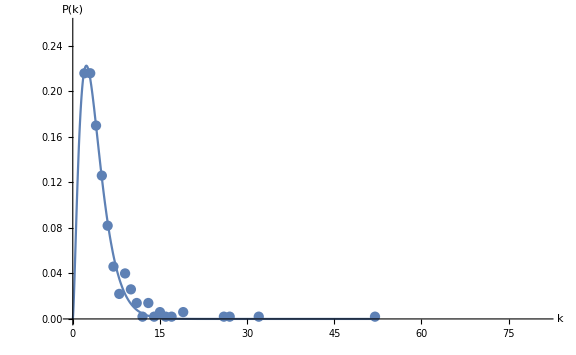

```mathematica
fibOrbitsNVPlot=Show[
ListPlot[fibOrbitsNVDegrees,PlotRange->{{0,81},{0,0.259}},AxesOrigin->{0,0}],
Plot[fibOrbitsNVNlm[x],{x,0,Max[Keys[fibOrbitsNVDegrees]]},PlotRange->{{0,81},{0,0.26}},AxesOrigin->{0,0}],
AxesLabel-> {Style["k",36, Italic],Style["P(k)", 36,Italic]},LabelStyle->20,ImageSize->Large
]
```

```mathematica
fibOrbitsNVNlm["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
γ | -1.54319 | 0.23035 | {-2.02713,-1.05924}
c | 0.281047 | 0.0214747 | {0.235931,0.326164}
d | 0.66026 | 0.0627234 | {0.528483,0.792037}

```mathematica
TableForm[Flatten[{"natural visibility",Mean@ VertexDegree[fibOrbitsNVGraph]//N,MeanGraphDistance[fibOrbitsNVGraph]//N,
GlobalClusteringCoefficient[fibOrbitsNVGraph]//N,Mean[fibOrbitsNVNlm["FitResiduals"]^2],ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@fibOrbitsNVNlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}],TableHeadings->{{"algo","⟨k⟩","⟨l_min⟩","C_c","⟨e^2⟩","γ","C","δ"}, None},TableDirections->Row]
```

algo | ⟨k⟩ | ⟨l_min⟩ | C_c | ⟨e^2⟩ | γ | C | δ
natural visibility | 4.932 | 4.73492 | 0.338099 | 0.0000502013 | -1.54319 ± 0.483947 | 0.281047 ± 0.0451167 | 0.66026 ± 0.131777

## Horizontal Visibility

```mathematica
fibOrbitsHVLinks=horizontalVisibility[];
```

```mathematica
fibOrbitsHVGraph=Graph[fibOrbitsHVLinks,DirectedEdges->False,GraphLayout->"CircularEmbedding"];
```

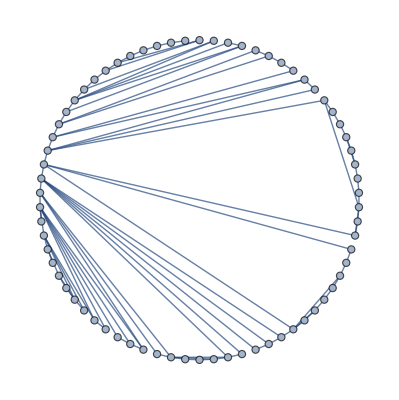

```mathematica
Graph[fibOrbitsHVLinks[[;;100]],DirectedEdges->False,GraphLayout->"CircularEmbedding"]
```

```mathematica
fibOrbitsHVDegrees=Counts[VertexDegree[fibOrbitsHVGraph]]/Length@VertexDegree[fibOrbitsHVGraph]
```

<|1→1/500,2→119/250,3→129/500,5→2/25,4→63/500,7→3/250,8→1/100,6→9/250|>

```mathematica
fibOrbitsHVDegrees[1]=.
```

```mathematica
data=Table[{x,fibOrbitsHVDegrees[x]},{x,Keys[fibOrbitsHVDegrees]}];
fibOrbitsHVNlm=NonlinearModelFit[data,c k^-γ E^(-d k),{{γ,2},{c,3},{d,0}},k]
```

FittedModel[1.68919 ⅇ^(-0.695959 k) k^0.181538]

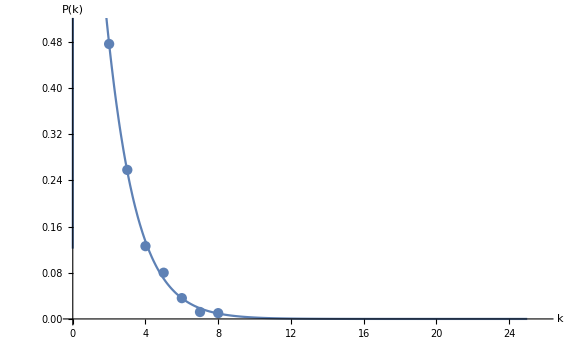

```mathematica
fibOrbitsHVPlot=Show[
ListPlot[fibOrbitsHVDegrees,PlotRange->{{0,25.9},{0,.51}},AxesOrigin->{0,0}],Plot[fibOrbitsHVNlm[x],{x,0,25},PlotRange->Full,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",36, Italic],Style["P(k)", 36,Italic]},LabelStyle->20,ImageSize->Large
]
```

```mathematica
fibOrbitsHVNlm["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
γ | -0.181538 | 0.336459 | {-1.1157,0.752621}
c | 1.68919 | 0.0793153 | {1.46897,1.9094}
d | 0.695959 | 0.114714 | {0.377461,1.01446}

```mathematica
TableForm[
Flatten[{"horizontal visibility",Mean@ VertexDegree[fibOrbitsHVGraph]//N,MeanGraphDistance[fibOrbitsHVGraph]//N,
GlobalClusteringCoefficient[fibOrbitsHVGraph]//N,Mean[fibOrbitsHVNlm["FitResiduals"]^2],ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@fibOrbitsHVNlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}],TableHeadings->{{"algo","⟨k⟩","⟨l_min⟩","C_c","⟨e^2⟩","γ","C","δ"},None},TableDirections->Row]
```

algo | ⟨k⟩ | ⟨l_min⟩ | C_c | ⟨e^2⟩ | γ | C | δ
horizontal visibility | 3.012 | 21.3108 | 0.264569 | 0.0000316638 | -0.181538 ± 0.934159 | 1.68919 ± 0.220215 | 0.695959 ± 0.318498

## Final Results

```mathematica
TableForm[{Flatten[{"natural visibility",Mean@ VertexDegree[fibNVGraph]//N,MeanGraphDistance[fibNVGraph]//N,
GlobalClusteringCoefficient[fibNVGraph]//N,Mean[fibNVNlm["FitResiduals"]^2],ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@fibNVNlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}],
Flatten[{"horizontal visibility",Mean@ VertexDegree[fibHVGraph]//N,MeanGraphDistance[fibHVGraph]//N,
GlobalClusteringCoefficient[fibHVGraph]//N,Mean[fibHVNlm["FitResiduals"]^2],ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@fibHVNlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}],Flatten[{"natural visibility",Mean@ VertexDegree[fibOrbitsNVGraph]//N,MeanGraphDistance[fibOrbitsNVGraph]//N,
GlobalClusteringCoefficient[fibOrbitsNVGraph]//N,Mean[fibOrbitsNVNlm["FitResiduals"]^2],ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@fibOrbitsNVNlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}],Flatten[{"horizontal visibility",Mean@ VertexDegree[fibOrbitsHVGraph]//N,MeanGraphDistance[fibOrbitsHVGraph]//N,
GlobalClusteringCoefficient[fibOrbitsHVGraph]//N,Mean[fibOrbitsHVNlm["FitResiduals"]^2],ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@fibOrbitsHVNlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]},TableHeadings->{None,{"algo","⟨k⟩","⟨l_min⟩","C_c","⟨e^2⟩","γ","C","δ"}}]
```

algo | ⟨k⟩ | ⟨l_min⟩ | C_c | ⟨e^2⟩ | γ | C | δ
natural visibility | 14.188 | 2.08964 | 0.141642 | 0.0000512414 | -6.00465 ± 1.02051 | 0.000271497 ± 0.000296404 | 0.80616 ± 0.128777
horizontal visibility | 3.708 | 9.26409 | 0.301998 | 0.0000285214 | 0.490378 ± 0.43927 | 1.20566 ± 0.110359 | 0.379862 ± 0.135665
natural visibility | 4.932 | 4.73492 | 0.338099 | 0.0000502013 | -1.54319 ± 0.483947 | 0.281047 ± 0.0451167 | 0.66026 ± 0.131777
horizontal visibility | 3.012 | 21.3108 | 0.264569 | 0.0000316638 | -0.181538 ± 0.934159 | 1.68919 ± 0.220215 | 0.695959 ± 0.318498